# De ecuaciones a código

## Funciones y su aplicación

## Creación de funciones

### Asignaciones

```mathematica
Now
```

Sun 27 Jul 2025 16:51:16GMT-6

Asignaciones «inmediatas»

```mathematica
ahora1=Now
```

Sun 27 Jul 2025 16:51:18GMT-6

Asignaciones «retrasadas»

```mathematica
ahora2:=Now
```

Comparación

```mathematica
{Now,ahora1,ahora2}
```

{Sun 27 Jul 2025 16:51:18GMT-6,Sun 27 Jul 2025 16:51:18GMT-6,Sun 27 Jul 2025 16:51:18GMT-6}

### Funciones

```mathematica
FunF[x_]:=6+7x^2
```

```mathematica
FunF[19.3]
```

2613.43

```mathematica
FunG=Function[x,6+7x^2]
```

Function[x,6+7 x^2]

```mathematica
FunG[19.3]
```

2613.43

```mathematica
FunH=x|->6+7x^2
```

Function[x,6+7 x^2]

```mathematica
FunH[19.3]
```

2613.43

```mathematica
FunI=6+7#^2&
```

6+7 #1^2&

```mathematica
FunI[19.3]
```

2613.43

## Multiple dispatch

### Patrones

```mathematica
test={f[x],1,f[7],2.5,g[Pi],6/7,f[100,200,300],3.5,f[],4,h[],I,f[6]};
```

```mathematica
Cases[test,4]
```

{4}

```mathematica
Cases[test,_]
```

{f[x],1,f[7],2.5,g[π],6/7,f[100,200,300],3.5,f[],4,h[],ⅈ,f[6]}

```mathematica
Cases[test,_Real]
```

{2.5,3.5}

```mathematica
Cases[test,f[_]]
```

{f[x],f[7],f[6]}

```mathematica
Cases[test,(f|g)[_]]
```

{f[x],f[7],g[π],f[6]}

```mathematica
Cases[test,f[__]]
```

{f[x],f[7],f[100,200,300],f[6]}

```mathematica
Cases[test,f[___]]
```

{f[x],f[7],f[100,200,300],f[],f[6]}

```mathematica
Cases[test,(_Integer|_Rational)]
```

{1,6/7,4}

```mathematica
Cases[test,_?NumericQ]
```

{1,2.5,6/7,3.5,4,ⅈ}

```mathematica
Cases[test,f[6|7]]
```

{f[7],f[6]}

### Definición de funciones avanzada

#### Patrones básicos

```mathematica
FunA[x_,y_]:=x+y
```

```mathematica
FunA[7,6]
```

13

```mathematica
FunA[a,1]
```

1+a

```mathematica
FunA[{1,2,3},4]
```

{5,6,7}

```mathematica
FunB[x_Integer,y_Integer]:=x+y
```

```mathematica
FunB[7,6]
```

13

```mathematica
FunB[a,1]
```

FunB[a,1]

```mathematica
FunB[{1,2,3},4]
```

FunB[{1,2,3},4]

```mathematica
FunB[π,ⅈ]
```

FunB[π,ⅈ]

```mathematica
FunC[x_Complex,y_Complex]:=x+y
```

```mathematica
FunC[1,2]
```

FunC[1,2]

```mathematica
FunD[x_?NumericQ,y_?NumericQ]:=x+y
```

```mathematica
FunD[1,1/2]
```

3/2

```mathematica
FunD[1/2,2.4]
```

2.9

```mathematica
FunD[2.4,ⅈ]
```

2.4+1. ⅈ

```mathematica
FunD[a,b]
```

FunD[a,b]

#### Patrones intermedios

```mathematica
FunE[x_MiDato,y_MiOtroDato]:=x+y
```

```mathematica
FunE[1,2]
```

FunE[1,2]

```mathematica
MiDato[1]
```

MiDato[1]

```mathematica
MiOtroDato[2]
```

MiOtroDato[2]

```mathematica
FunE[MiDato[1],MiOtroDato[2]]
```

MiDato[1]+MiOtroDato[2]

```mathematica
FunZ[MiDato[x_],MiOtroDato[y_]]:=x+y
```

```mathematica
FunZ[MiDato[1],MiOtroDato[2]]
```

3

```mathematica
FunY[{{{x_},{}},y_}]:=x+y
```

```mathematica
FunY[{{{1},{}},2}]
```

3

```mathematica
FunX[{x_,_,y_}]:=x+y
```

```mathematica
FunX[{1,a,9}]
```

10

```mathematica
FunW[{x_,__,y_}]:=x+y
```

```mathematica
FunW[{1,2,3,4,5,6,7,8,9}]
```

10

```mathematica
FunW[{1,2}]
```

FunW[{1,2}]

```mathematica
FunV[{x_,___,y_}]:=x+y
```

```mathematica
FunV[{1,2,3,4,5,6,7,8,9}]
```

10

```mathematica
FunV[{1,2}]
```

3

```mathematica
FunU[x_,y_]:=x+y/;x<y
```

```mathematica
FunU[9,1]
```

FunU[9,1]

```mathematica
FunU[1,9]
```

10

### Multiple dispatch

```mathematica
Fun[n_Integer]:=Range[0,n,Sign[n]]
```

```mathematica
Fun[n_Rational]:={Numerator[n],Denominator[n]}
```

```mathematica
Fun[n_Real]:=n-Round[n]
```

```mathematica
Fun[n_Complex]:={Re[n],Im[n]}
```

```mathematica
Fun["Hola mundo"]:="Adios"
```

```mathematica
Fun[n_?NumericQ,m_?NumericQ]:=n/m/;m!=0
```

```mathematica
Fun[-5]
```

{0,-1,-2,-3,-4,-5}

```mathematica
Fun[1/3]
```

{1,3}

```mathematica
Fun[1.4]
```

0.4

```mathematica
Fun[ⅈ]
```

{0,1}

```mathematica
Fun["Hola mundo"]
```

Adios

```mathematica
Fun[3,4]
```

3/4

#### Ejemplo real

```mathematica
Fib[0]:=0
```

```mathematica
Fib[1]:=1
```

```mathematica
Fib[n_]:=Fib[n-1]+Fib[n-2]
```

```mathematica
Fib[10]
```

55

```mathematica
Fib[1.1]
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

TerminatedEvaluation[RecursionLimit]+Fib[1.1-2]

```mathematica
Fib[-1]
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

TerminatedEvaluation[RecursionLimit]+Fib[-1-2]

```mathematica
Fib[n_]=.
```

```mathematica
Fib[n_Integer]:=Fib[n-1]+Fib[n-2]/;n>=0
```

```mathematica
Fib[10]
```

55

```mathematica
Fib[1.1]
```

Fib[1.1]

```mathematica
Fib[-1]
```

Fib[-1]

## Ejemplos

### Atrapando agua de lluvia

#### Código

Definiendo una visualización para el problema

```mathematica
PlotWater[h_List]:=BarChart[#,
   ChartLayout->"Stacked",
   AspectRatio->Automatic,
   Ticks->{None,None},
   AxesOrigin->{0.5,0},
   BarSpacing->None,
   ChartStyle->({Directive[Black,#],Directive[Blue,#]}&@EdgeForm[None])
  ]&@
 Transpose[{h,-h+Min/@Transpose@{FoldList[Max,h],Reverse@FoldList[Max,Reverse@h]}}]
```

Calcular agua atrapada (con recursión de cola)

```mathematica
TailWater[{},w_]:=w
TailWater[{_},w_]:=w
TailWater[{_,_},w_]:=w
TailWater[h_List,w_]:=TailWater[Prepend[Drop[h,2],Max[Take[h,2]]],w+Max[0,Subtract@@Take[h,2]]]/;First[h]<Last[h]
TailWater[h_List,w_]:=TailWater[Append[Drop[h,-2],Max[Take[h,-2]]],w+Max[0,Subtract@@Reverse@Take[h,-2]]]
```

Definición práctica

```mathematica
Water[h_List]:=TailWater[h,0]
```

#### Ejecución

```mathematica
heights={0,1,0,2,1,0,1,3,2,1,2,1}
```

{0,1,0,2,1,0,1,3,2,1,2,1}

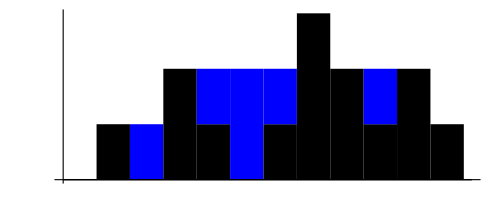

```mathematica
PlotWater[heights]
```

```mathematica
Water[heights]
```

6